# Chebyshev Bias

### Author

Eric W. Weisstein
April 12, 2011

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PrimeNumbers/ChebyshevBias.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/ChebyshevBias.html.

©2011 Wolfram Research, Inc. except for portions noted otherwise

## By 3

```mathematica
a3=Accumulate[If[Mod[#,3]==1,-1,1]&/@Prime[Range[10^5]]];//Timing
```

{0.131738,Null}

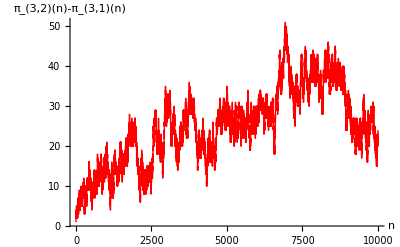

```mathematica
g1=ListPlot[Take[a3,10^4],AxesLabel->{n,Subscript[Pi,Row[{3,",",2}]][Prime[n]]-Subscript[Pi,Row[{3,",",1}]][Prime[n]]},Joined->True,PlotStyle->Red]
```

Old code

```mathematica
1+Position[Rest[FoldList[Plus,0,Mod[Prime[Range[2,10^5]],4]/. 3->-1]],0]//Flatten//Timing
```

{1.15 Second,{3,7,13,89,2943,2945,2947,2949,2951,2953,50371,50375,50377,50379,50381,50393,50413,50423,50425,50427,50429,50431,50433,50435,50437,50439,50445,50449,50451,50503,50507,50515,50517,50821,50843,50853,50855,50857,50859,50861,50865,50893,50899,50901,50903,50905,50907,50909,50911,50913,50915,50917,50919,50921,50927,50929,51119,51121,51123,51127,51151,51155,51157,51159,51161,51163,51177,51185,51187,51189,51195,51227,51261,51263,51285,51287,51289,51291,51293,51297,51299,51319,51321,51389,51391,51395,51397,51505,51535,51537,51543,51547,51551,51553,51557,51559,51567,51573,51575,51577,51595,51599,51607,51609,51611,51615,51617,51619,51621,51623,51627}}

## By 4

Must take p==2 into account:

```mathematica
a4=Prepend[Accumulate[If[Mod[#,4]==1,-1,1]&/@Prime[Range[2,10^5]]],0];//Timing
```

{0.127147,Null}

{0.12388,Null}

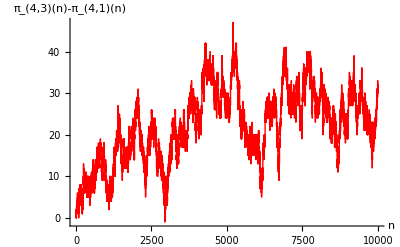

```mathematica
g2=ListPlot[Take[a4,10^4],AxesLabel->{n,Subscript[Pi,Row[{4,",",3}]][Prime[n]]-Subscript[Pi,Row[{4,",",1}]][Prime[n]]},Joined->True,PlotStyle->Red]
```

https://oeis.org/A096628

```mathematica
Position[a4,_?Negative]//Flatten
```

{2,4,5,6,8,9,10,11,12,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,«99571»,99962,99963,99964,99965,99966,99967,99968,99969,99970,99971,99972,99973,99974,99975,99976,99977,99978,99979,99980,99981,99982,99983,99984,99985,99986,99987,99988,99989,99990,99991,99992,99993,99994,99995,99996,99997,99998,99999,100000}

```mathematica
Position[a4,0]//Flatten
```

{1,3,7,13,89,2943,2945,2947,2949,2951,2953,50371,50375,50377,50379,50381,50393,50413,50423,50425,50427,50429,50431,50433,50435,50437,50439,50445,50449,50451,50503,50507,50515,50517,50821,50843,50853,50855,50857,50859,50861,50865,50893,50899,50901,50903,50905,50907,50909,50911,50913,50915,50917,50919,50921,50927,50929,51119,51121,51123,51127,51151,51155,51157,51159,51161,51163,51177,51185,51187,51189,51195,51227,51261,51263,51285,51287,51289,51291,51293,51297,51299,51319,51321,51389,51391,51395,51397,51505,51535,51537,51543,51547,51551,51553,51557,51559,51567,51573,51575,51577,51595,51599,51607,51609,51611,51615,51617,51619,51621,51623,51627}

```mathematica
Position[a4,_?Positive]//Flatten
```

{2946,50378,50380,50382,50383,50384,50385,50386,50387,50388,50389,50390,50391,50392,50414,50415,50416,50417,50418,50419,50420,50421,50422,50424,50426,50428,50430,50436,50438,50446,50447,50448,50450,50822,50823,50824,50825,50826,50827,50828,50829,50830,50831,50832,50833,50834,50835,50836,50837,50838,50839,50840,50841,50842,50844,50845,50846,50847,50848,50849,50850,50851,50852,50854,50856,50858,50862,50863,50864,50866,50867,50868,50869,50870,50871,50872,50873,50874,50875,50876,50877,50878,50879,50880,50881,50882,50883,50884,50885,50886,50887,50888,50889,50890,50891,50892,50902,50904,50906,50908,50916,50918,50920,50928,51120,51122,51152,51153,51154,51158,51160,51178,51179,51180,51181,51182,51183,51184,51186,51188,51196,51197,51198,51199,51200,51201,51202,51203,51204,51205,51206,51207,51208,51209,51210,51211,51212,51213,51214,51215,51216,51217,51218,51219,51220,51221,51222,51223,51224,51225,51226,51262,51264,51265,51266,51267,51268,51269,51270,51271,51272,51273,51274,51275,51276,51277,51278,51279,51280,51281,51282,51283,51284,51286,51294,51295,51296,51300,51301,51302,51303,51304,51305,51306,51307,51308,51309,51310,51311,51312,51313,51314,51315,51316,51317,51318,51392,51393,51394,51552,51558,51568,51569,51570,51571,51572,51574,51576,51578,51579,51580,51581,51582,51583,51584,51585,51586,51587,51588,51589,51590,51591,51592,51593,51594,51596,51597,51598,51600,51601,51602,51603,51604,51605,51606,51612,51613,51614,51622}

Old code

```mathematica
1+Position[Rest[FoldList[Plus,0,Mod[Prime[Range[2,10^5]],4]/. 3->-1]],_?Positive]//Flatten//Timing
```

{1.54 Second,{2946,50378,50380,50382,50383,50384,50385,50386,50387,50388,50389,50390,50391,50392,50414,50415,50416,50417,50418,50419,50420,50421,50422,50424,50426,50428,50430,50436,50438,50446,50447,50448,50450,50822,50823,50824,50825,50826,50827,50828,50829,50830,50831,50832,50833,50834,50835,50836,50837,50838,50839,50840,50841,50842,50844,50845,50846,50847,50848,50849,50850,50851,50852,50854,50856,50858,50862,50863,50864,50866,50867,50868,50869,50870,50871,50872,50873,50874,50875,50876,50877,50878,50879,50880,50881,50882,50883,50884,50885,50886,50887,50888,50889,50890,50891,50892,50902,50904,50906,50908,50916,50918,50920,50928,51120,51122,51152,51153,51154,51158,51160,51178,51179,51180,51181,51182,51183,51184,51186,51188,51196,51197,51198,51199,51200,51201,51202,51203,51204,51205,51206,51207,51208,51209,51210,51211,51212,51213,51214,51215,51216,51217,51218,51219,51220,51221,51222,51223,51224,51225,51226,51262,51264,51265,51266,51267,51268,51269,51270,51271,51272,51273,51274,51275,51276,51277,51278,51279,51280,51281,51282,51283,51284,51286,51294,51295,51296,51300,51301,51302,51303,51304,51305,51306,51307,51308,51309,51310,51311,51312,51313,51314,51315,51316,51317,51318,51392,51393,51394,51552,51558,51568,51569,51570,51571,51572,51574,51576,51578,51579,51580,51581,51582,51583,51584,51585,51586,51587,51588,51589,51590,51591,51592,51593,51594,51596,51597,51598,51600,51601,51602,51603,51604,51605,51606,51612,51613,51614,51622}}

## Combined Plot

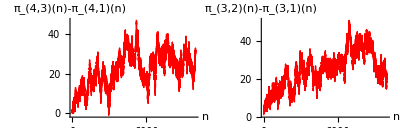

```mathematica
GraphicsRow[{g2,g1},Spacings->-30,ImageSize->400]
```